```mathematica
Clear["Global`*"]
```

```mathematica
subslist={wHH->(v-c)/2,wHD->v,wDH->0,wDD->v/2};
```

## Mutant transition matrix

b_11: contribution of hawk to hawk etc

```mathematica
B=1/λ{
{(u1 wHH+(1-u1)wHD)+phatH,(u1 wDH+(1-u1)wDD)+1-phatD},
{(u1 wHH+(1-u1)wHD)+1-phatH,(u1 wDH+(1-u1)wDD)+phatD} 
}/.subslist;
```

## Resident transition matrix

```mathematica
A=B/.{phatD->pD,phatH->pH,λ->1}
```

{{pH+(1-u1) v+1/2 u1 (-c+v),1-pD+1/2 (1-u1) v},{1-pH+(1-u1) v+1/2 u1 (-c+v),pD+1/2 (1-u1) v}}

## Eigenvectors

Eigenvalues

```mathematica
eigvecs=Solve[{CharacteristicPolynomial[A,λ]==0,
λ u1==A[[1,1]]u1+A[[1,2]](1-u1),
λ v1==A[[1,1]]v1+A[[2,1]]v2,
v1 u1+v2(1-u1)==1},{λ,u1,v1,v2}]
```

{{λ→(-2 c+2 c pD-2 v-c v+2 pD v+2 pH v+v^2)/(2 v),u1→(2-2 pD+v)/v,v1→-(v (2-2 pD+v) (128 c-32 c^2+2 c^3-192 c pD+54+24 c v^3+40 pD v^3+24 pH v^3-16 v^4))/(-512 c+128 c^2-8 c^3+1792 c pD-704 c^2 pD+158+128 v^5-24 c v^5-104 pD v^5-24 pH v^5+16 v^6),v2→0},2,{λ→1/1,2,v2→1}}
 |  |  |  |

```mathematica
v2/.eigvecs/.{c->3.0,v->1.0,pD->0.5,pH->0.9}
```

{0,0.763046-0.607517 ⅈ,0.417175+0. ⅈ,0.763046+0.607517 ⅈ}

```mathematica
FindRoot[{CharacteristicPolynomial[A,λ]==0,
λ u1==A[[1,1]]u1+A[[1,2]](1-u1),
λ v1==A[[1,1]]v1+A[[2,1]]v2,
v1 u1+v2(1-u1)==1}/.{v->1.0,c->3.0,pD->0.1,pH->0.9},{{λ,1.0},{u1,0.5},{v1,1},{v2,1}}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{λ→0.954288,u1→0.536762,v1→0.514261,v2→1.55497}

```mathematica
lsol=Solve[{CharacteristicPolynomial[A,λ]==0,λ u1==A[[1,1]]u1+A[[1,2]](1-u1)},{λ,u1}];
```

```mathematica
Table[λ/.lsol/.{pD->pdx,pH->phx,v->1.0,c->2.0},{pdx,0,1.0,0.1},{phx,0,1.0,0.1}]
```

```mathematica
Reduce[{D[(λ/.lsol[[1]]),pD]<1,c>v}]
```

v<0&&c>0

```mathematica
lsol[[2]]/.{v->1.0,c->3.0,pD->0.1,pH->0.9}
```

{λ→0.77057+1.02709 ⅈ,u1→0.686954-0.249189 ⅈ}

```mathematica
Eigenvectors[A][[1]].Eigenvectors[Transpose[A]][[1]]//Simplify
```

1+(2 pD-2 pH+c u1-v+√(4 pD^2+4 pH^2-4 pH (4+c u1+v-2 u1 v)+4 pD (-4+2 pH+3 c u1-5 v+2 u1 v)+(-4+c u1-3 v+2 u1 v)^2))^2/(4 (-2+2 pD+(-1+u1) v) (-2+2 pH+c u1-2 v+u1 v))

## Selection gradients

```mathematica
dWdpD=v1 u1 D[B[[1,1]],phatD]+v1 (1-u1)D[B[[1,2]],phatD]+v2 u1 D[B[[2,1]],phatD]+v2 (1-u1) D[B[[2,2]],phatD];
```

```mathematica
dWdpH=v1 u1 D[B[[1,1]],phatH]+v1 (1-u1)D[B[[1,2]],phatH]+v2 u1 D[B[[2,1]],phatH]+v2 (1-u1) D[B[[2,2]],phatH];
```

```mathematica
test=ConstantArray[0,{6,2}];
```

```mathematica
test[[5;;6,1]]
```

{0,0}

## Numerical solving

```mathematica
ans[{vs_,cs_,tend_,pdinit_,phinit_}]:=Module[{Data,iter,eigvecs,eigvecssol,pdt,pht},
Data=ConstantArray[0,{6,tend}];
eigvecs={CharacteristicPolynomial[A,λ]==0,
λ u1==A[[1,1]]u1+A[[1,2]](1-u1),
λ v1==A[[1,1]]v1+A[[2,1]]v2,
v1 u1+v2(1-u1)==1}/.{v->vs,c->cs};
Data[[5;;6,1]]={pdinit,phinit};
For[iter=2,iter≤tend,iter++,
pdt=Data[[5,iter-1]];
pht=Data[[6,iter-1]];
eigvecssol=FindRoot[eigvecs/.{pD->pdt,pH->pht},{{λ,1},{u1,0.5},{v1,1},{v2,1}}];
Data[[All,iter]]=Join[({λ,u1,v1,v2}/.eigvecssol),{Clip[pdt+0.005*(dWdpD/.eigvecssol/.{v->vs,c->cs}),{0,1}],
Clip[pht+0.005*(dWdpH/.eigvecssol/.{v->vs,c->cs}),{0,1}]}];
];
Return[Data];
];
```

```mathematica
all=ans[{1.0,3.0,10000,0.8,0.2}];
```

```mathematica
all[[5;;6,-1]]
```

{0.773202,0.21307}

```mathematica
ListLinePlot[all[[5;;6,All]]]
```

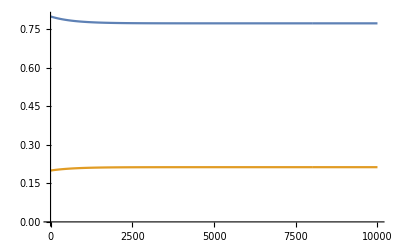

```mathematica
selgrad[{vs_,cs_,pdinit_,phinit_}]:=Module[{veccies},
veccies=FindRoot[{CharacteristicPolynomial[A,λ]==0,
λ u1==A[[1,1]]u1+A[[1,2]](1-u1),
λ v1==A[[1,1]]v1+A[[2,1]]v2,
v1 u1+v2(1-u1)==1}/.{v->vs,c->cs,pD->pdinit,pH->phinit},{{λ,1},{u1,0.5},{v1,1},{v2,1}}];
Return[{dWdpD/.veccies/.{v->vs,c->cs,pD->pdinit,pH->phinit},dWdpH/.veccies/.{v->vs,c->cs,pD->pdinit,pH->phinit}}]
]
```

```mathematica
selgrad[{1.0,3.0,0.808316,0.283299}]
```

{4.43586×10^-8,-2.21793×10^-8}

FindRoot::nlnum: The function value {-0.5+0.5 pHx,0.5-0.5 (1.25-1. pDx)-0.5 (0.+pHx),1.-1. (1.-1. pHx)-1. (0.+pHx),0.} is not a list of numbers with dimensions {4} at {λ,u1,v1,v2} = {1.,0.5,1.,1.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[{CharacteristicPolynomial[A,λ]==0,λ u1==Part[«3»] u1+Part[«3»] Plus[«2»],λ v1==Part[«3»] v1+Part[«3»] v2,v1 u1+v2 Plus[«2»]==1}/.{v→1.,c→3.,pD→pDx,pH→pHx},{{λ,1},{u1,0.5},{v1,1},{v2,1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {FindRoot[{CharacteristicPolynomial[A,λ]==0,λ u1==Part[«3»] u1+Part[«3»] Plus[«2»],λ v1==Part[«3»] v1+Part[«3»] v2,v1 u1+v2 Plus[«2»]==1}/.{1.→1.,3.→3.,pDx→pDx,pHx→pHx},{{λ,1},{u1,0.5},{v1,1},{v2,1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {FindRoot[{CharacteristicPolynomial[A,λ]==0,λ u1==Part[«3»] u1+Part[«3»] Plus[«2»],λ v1==Part[«3»] v1+Part[«3»] v2,v1 u1+v2 Plus[«2»]==1}/.{v→1.,c→3.,pD→pDx,pH→pHx},{{λ,1},{u1,0.5},{v1,1},{v2,1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

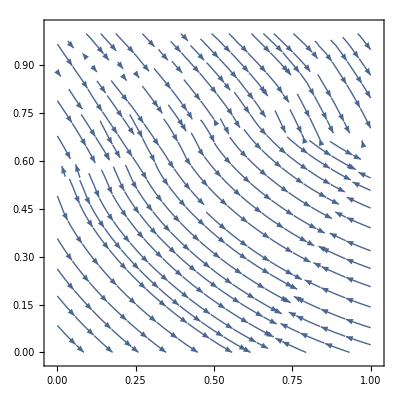

```mathematica
StreamPlot[selgrad[{1.0,3.0,pDx,pHx}],{pDx,0,1.0},{pHx,0,1.0}]
```

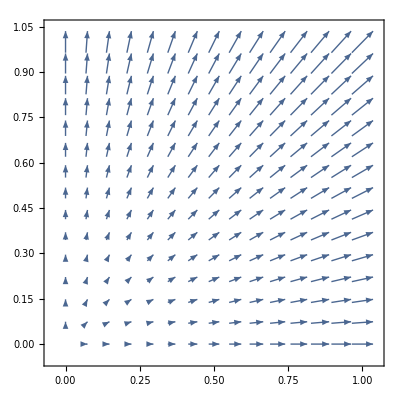

```mathematica
VectorPlot[{pDx,pHx,selgrad[{1.0,3.0,pDx,pjjHx}][[2]]},{pDx,0,1},{pHx,0,1}]
```